## Code st (PB21010452 肖羿)

1.【概括】

使用 Mathematica 绘制五阶 Adams-Bashforth 公式和五阶 Adams-Moulton 公式的绝对稳定性区域。

2.【基本原理】

Adams-Bashforth 公式：
多项式 ，
Adams-Moulton 公式：
多项式 ，
  在绝对稳定区域时， 的根满足 。

3.【结果展示】

5

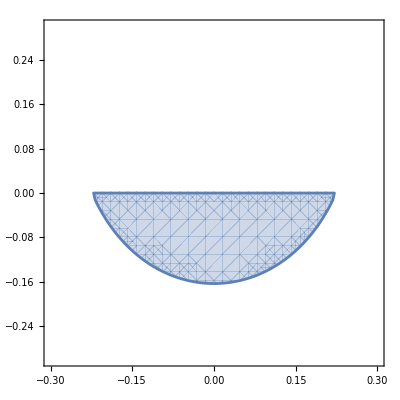

```mathematica
(*【Adams-Bashforth】*)
Clear[w,p,phi,z0]
w[x_,y_]:=x*I+y;(*ω=λ*);
p[z_]:=z^5-z^4;q[z_]:=1/720(1901 z^4-2774 z^3+2616 z^2-1274z+251);
phi[x_,y_,z_]:=p[z]-w[x,y]*q[z];
z0[x_,y_]:=NSolve[phi[x,y,z]==0,z]
m=Length[z0[a,b]]

RegionPlot[Norm[z0[a,b][[1,1,2]]]<1&&Norm[z0[a,b][[2,1,2]]]<1&&Norm[z0[a,b][[3,1,2]]]<1&&Norm[z0[a,b][[4,1,2]]]<1&&Norm[z0[a,b][[5,1,2]]]<1,{a,-0.3,0.3},{b,-0.3,0.3}]
```

4

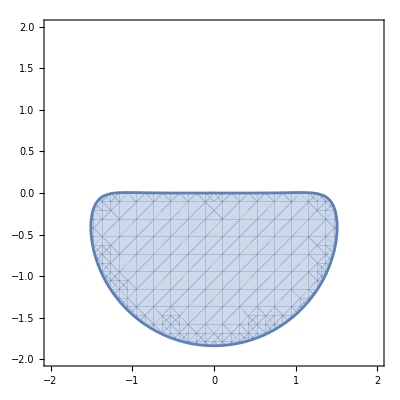

```mathematica
(*【Adams-Moulton】*)
Clear[w,p,phi,z0]
w[x_,y_]:=x*I+y;(*ω=λ*);
p[z_]:=z^4-z^3;q[z_]:=1/720(251 z^4+646 z^3-264 z^2+106z-19);
phi[x_,y_,z_]:=p[z]-w[x,y]*q[z];
z0[x_,y_]:=NSolve[phi[x,y,z]==0,z]
m=Length[z0[a,b]]

RegionPlot[Norm[z0[a,b][[1,1,2]]]<1&&Norm[z0[a,b][[2,1,2]]]<1&&Norm[z0[a,b][[3,1,2]]]<1&&Norm[z0[a,b][[4,1,2]]]<1,{a,-2,2},{b,-2,2}]
```